```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.2,Jtwo,-0.1,z]-G22[1,0.2,Jtwo,-0.1,z]-G12[1,0.2,Jtwo,-0.1,z]^2+G11[1,0.2,Jtwo,-0.1,z]G22[1,0.2,Jtwo,-0.1,z]
FindRoot[Nulls[0.,z]==0,{z,0.7536715765093541}]
```

{z→0.753672}

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[-1,-0.005,0.7536715765093541]]
```

{{-0.005,0.748483},{-0.01,0.743114},{-0.015,0.737576},{-0.02,0.731879},{-0.025,0.726033},{-0.03,0.720046},{-0.035,0.713924},{-0.04,0.707673},{-0.045,0.701298},{-0.05,0.694803},{-0.055,0.68819},{-0.06,0.681461},{-0.065,0.67462},{-0.07,0.667666},{-0.075,0.660599},{-0.08,0.653421},{-0.085,0.646131},{-0.09,0.638728},{-0.095,0.63121},{-0.1,0.623576}}

```mathematica
moduler[Lister[1,0.005,0.7536715765093541]]
```

{{0.005,0.758665},{0.01,0.763448},{0.015,0.768003},{0.02,0.772313},{0.025,0.776357},{0.03,0.780115},{0.035,0.783565},{0.04,0.786687},{0.045,0.789461},{0.05,0.79187},{0.055,0.793898},{0.06,0.795536},{0.065,0.796776},{0.07,0.797616},{0.075,0.798058},{0.08,0.798109},{0.085,0.797779},{0.09,0.797081},{0.095,0.796031},{0.1,0.794646}}

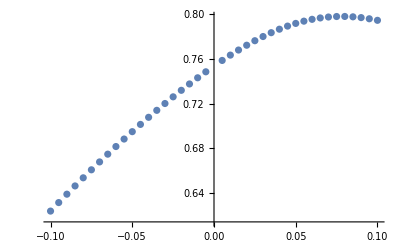

```mathematica
P = ListPlot[{{-0.005,0.7484834098231707},{-0.01,0.7431140795450425},{-0.015,0.7375757378693601},{-0.02,0.7318790089540628},{-0.025,0.7260330935826821},{-0.03,0.7200458852984055},{-0.035,0.7139240888131906},{-0.04,0.7076733346013035},{-0.045,0.701298285933513},{-0.05,0.6948027362988493},{-0.055,0.6881896963223565},{-0.06,0.6814614700458248},{-0.065,0.6746197209042067},{-0.07,0.6676655280468112},{-0.075,0.6605994333068429},{-0.08,0.6534214807725982},{-0.085,0.6461312476330291},{-0.09,0.6387278689614306},{-0.095,0.6312100557660517},{-0.1,0.6235761071573053},{0.005,0.758664819246358},{0.01,0.7634477314478979},{0.015,0.7680032863802935},{0.02,0.7723129532088566},{0.025,0.7763569302391824},{0.03,0.7801145197103546},{0.035,0.7835646592496984},{0.04,0.7866866080425511},{0.045,0.7894607612579949},{0.05,0.7918695375424517},{0.055,0.7938982578891333},{0.06,0.79553591832393},{0.065,0.7967757610431646},{0.07,0.7976155717130281},{0.075,0.7980576705282044},{0.08,0.7981086111893011},{0.085,0.797778642880953},{0.09,0.797081016013443},{0.095,0.796031219300202},{0.1,0.794646226161407}}]
```

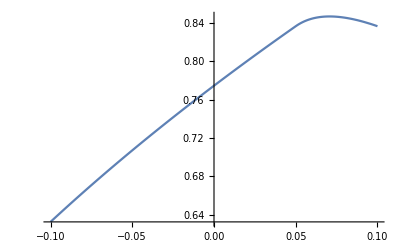

```mathematica
G = Plot[Sqrt[1+2(0.2*Cos[Inv[0.2,J]]+J*Cos[2*Inv[0.2,J]])],{J,-0.1,0.1}]
```

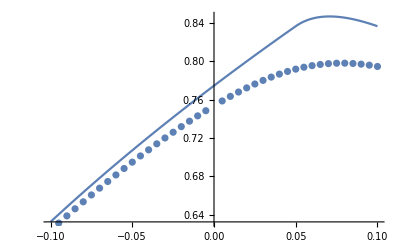

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0.2,moduler[Lister[-1,-0.005,0.7536715765093541]]]
```

{{-0.005,0.0196312},{-0.01,0.0184632},{-0.015,0.0174077},{-0.02,0.0164525},{-0.025,0.0155868},{-0.03,0.014801},{-0.035,0.0140869},{-0.04,0.0134369},{-0.045,0.0128446},{-0.05,0.012304},{-0.055,0.0118103},{-0.06,0.0113589},{-0.065,0.0109457},{-0.07,0.0105675},{-0.075,0.010221},{-0.08,0.00990348},{-0.085,0.0096126},{-0.09,0.0093462},{-0.095,0.00910237},{-0.1,0.00887942}}

```mathematica
differ[1,0.2,moduler[Lister[1,0.005,0.7536715765093541]]]
```

{{0.005,0.0223601},{0.01,0.0239531},{0.015,0.0257221},{0.02,0.027687},{0.025,0.0298688},{0.03,0.0322893},{0.035,0.0349706},{0.04,0.0379345},{0.045,0.0412016},{0.05,0.432875},{0.055,0.0476371},{0.06,0.0490547},{0.065,0.049483},{0.07,0.0492273},{0.075,0.048504},{0.08,0.0474681},{0.085,0.0462314},{0.09,0.0448744},{0.095,0.0434548},{0.1,0.0420138}}

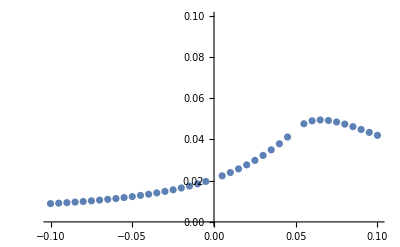

```mathematica
ListPlot[{{-0.005,0.019631164963690106},{-0.01,0.018463231041348283},{-0.015,0.017407705657714767},{-0.02,0.01645246840072556},{-0.025,0.015586755126884233},{-0.03,0.014801037536547934},{-0.035,0.014086900114861245},{-0.04,0.013436920491494364},{-0.045,0.012844556920772021},{-0.05,0.012304044887698318},{-0.055,0.011810303677643463},{-0.06,0.01135885298172612},{-0.065,0.010945739135897692},{-0.07,0.010567470265715584},{-0.075,0.010220959943094021},{-0.08,0.009903477298481733},{-0.085,0.009612604797170965},{-0.09,0.009346200879355337},{-0.095,0.009102367977233072},{-0.1,0.0088794248763705},{0.005,0.02236014834430744},{0.01,0.02395305595328323},{0.015,0.025722106939083722},{0.02,0.02768704679114331},{0.025,0.029868844590672516},{0.03,0.032289320753241424},{0.035,0.03497061793754652},{0.04,0.037934517080980945},{0.045,0.04120162503381253},{0.05,0.43287533384913723},{0.055,0.04763713541397563},{0.06,0.04905471229739844},{0.065,0.04948297371461985},{0.07,0.04922730458862512},{0.075,0.04850400275181521},{0.08,0.04746811507508708},{0.085,0.046231393301360724},{0.09,0.04487438000756294},{0.095,0.043454839014802404},{0.1,0.04201380037266855}}]
```

```mathematica
GLow[1,0.2,0.05001]
```

0.836672

```mathematica
GLow[1,0.2,0.055]
```

0.841535

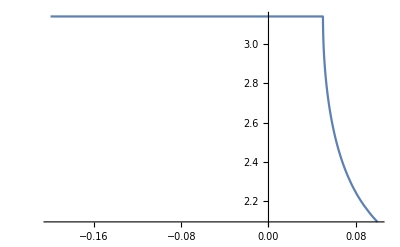

```mathematica
Plot[Inv[0.2,J],{J,-0.2,0.1}]
```